# Construction of the LS method for the Stochastic HIV Dynamics Model.

```mathematica
a:=0.5;
u:=5;
β:=10^(-8);
γ:=0.5;
η:=0.5;
NN:=100;
δ:=0.1;
λ:=10^6;
f1[{x_,y_,z_}]:= λ-δ*x-(1-γ)*β*x*z;
f2[{x_,y_,z_}]:=(1-γ)*β*x*z-a*y;f3[{x_,y_,z_}]:=(1-η)*NN*a*y-u*z-(1-γ)*β*x*z;
f[{x_,y_,z_}]:={f1[{x,y,z}],f2[{x,y,z}],f3[{x,y,z}]};
a1[{x_,y_,z_}]:=-δ-(1-γ)*β*z; 
a2[{x_,y_,z_}]:= -a;
a3[{x_,y_,z_}]:=-u -(1-γ)*β*x;
b1[{x_,y_,z_}]:=λ;
b2[{x_,y_,z_}]:=(1-γ)*β*x*z;
b3[{x_,y_,z_}]:= (1-η)*NN*a*y;
Fh1[{x_,y_,z_},ϵ_]:=x*Exp[ϵ*a1[{x,y,z}]];
Fh2[{x_,y_,z_},ϵ_]:=y*Exp[ϵ*a2[{x,y,z}]]+b2[{x,y,z}]*(Exp[-a*ϵ]-1)/-a;
Fh3[{x_,y_,z_},ϵ_]:=z*Exp[ϵ*a3[{x,y,z}]]+b3[{x,y,z}]*(Exp[ϵ*a3[{x,y,z}]]-1)/a3[{x,y,z}];
Fh[{x_,y_,z_},ϵ_]:={Fh1[{x,y,z},ϵ],Fh2[{x,y,z},ϵ],Fh3[{x,y,z},ϵ]};
```

```mathematica
Tx[{x_,y_,z_},ϵ_]:=1/ϵ^2*Integrate[(ϵ-Abs[x-ξ])*f1[{ξ,y,z}],{ξ,x-ϵ,x+ϵ}];
Ty[{x_,y_,z_},ϵ_]:=1/ϵ^2*Integrate[(ϵ-Abs[y-ξ])*f2[{x,ξ,z}],{ξ,y-ϵ,y+ϵ}];
Tz[{x_,y_,z_},ϵ_]:=1/ϵ^2*Integrate[(ϵ-Abs[z-ξ])*f3[{x,y,ξ}],{ξ,z-ϵ,z+ϵ}];
T[{x_,y_,z_},ϵ_]:=N[{Tx[{x,y,z},ϵ],Ty[{x,y,z},ϵ],Tz[{x,y,z},ϵ]}]
```

```mathematica
h=.5;
x0= 10000;
f[{x0,x0,x0}];
Norm[f[{x0,x0,x0}]-T[{x0,x0,x0},h]]
```

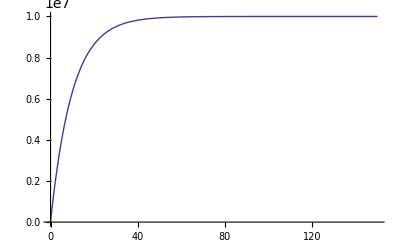

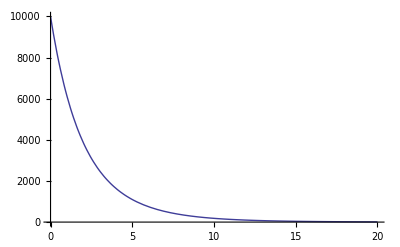

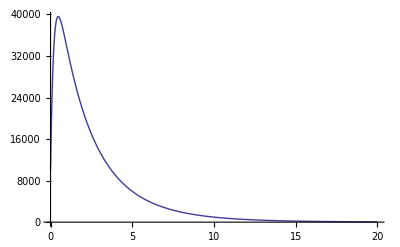

```mathematica
Sol=NDSolve[{
x'[t]==λ-δ*x[t]-(1-γ)*β*x[t]*z[t],
y'[t]==(1-γ)*β*x[t]*z[t]-a*y[t],
z'[t]==(1-η)*NN*a*y[t]-u*z[t]-(1-γ)*β*x[t]*z[t],
		x[0]==y[0]==z[0]==10000},{x,y,z},{t,150}
];
Plot[Evaluate[x[t]/.Sol],{t,0,150},PlotRange->All]
Plot[Evaluate[y[t]/.Sol],{t,0,20},PlotRange->All]
Plot[Evaluate[z[t]/.Sol],{t,0,20},PlotRange->All]
```

```mathematica
Clear[Euler];
Euler[T0_,K0_,Xzero0_]:=Module[
{T=T0,K=K0,Xzero=Xzero0},
h=N[T/K];
Ti=Table[0+(j-1)*h,{j,1,K+1}];
Y=Table[Xzero,{j,1,K+1}];
(*Print["i,\t Xstk[i]"];*)
For[j=1,j≤K,j++,
Y[[j+1]]=Y[[j]]+h*f[Y[[j]]];
(*Print[j,"\t",Y[[j]]];*)
];
Return[Transpose[{Ti,Y}]];
];
f[{x_,y_,z_}]:={
λ-δ*x-(1-γ)*β*x*z,
(1-γ)*β*x*z-a*y,
(1-η)*NN*a*y-u*z-(1-γ)*β*x*z
}
Xzero={10000,10000,10000};
Sol=Euler[150,2000,Xzero];
```

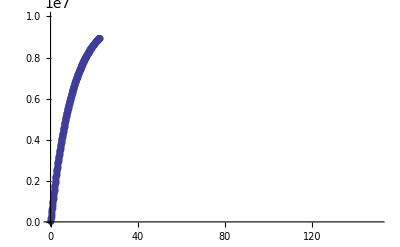

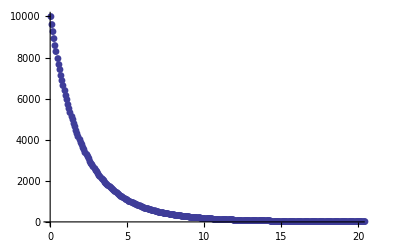

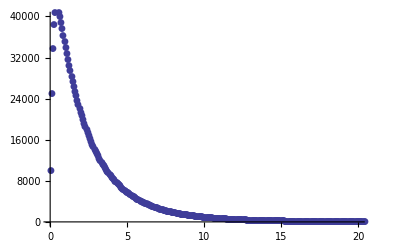

```mathematica
Xe1=Sol[[All,1]];
Ye1=Sol[[All,2,1]];
Xe2=Sol[[All,1]];
Ye2=Sol[[All,2,2]];
Xe3=Sol[[All,1]];
Ye3=Sol[[All,2,3]];
Sol1=Transpose[{Xe1[[1;;-1;;1]],Ye1[[1;;-1;;1]]}];
Sol2=Transpose[{Xe2[[1;;-1;;1]],Ye2[[1;;-1;;1]]}];
Sol3=Transpose[{Xe3[[1;;-1;;1]],Ye3[[1;;-1;;1]]}];
g1=ListPlot[
{Sol1},
PlotMarkers->Automatic,
PlotRange->{{0,150},{0,10^7}}
]
g2=ListPlot[
{Sol2},
PlotMarkers->Automatic,
PlotRange->{{0,20},{0,10000}}
]
g3=ListPlot[
{Sol3},
PlotMarkers->Automatic,
PlotRange->{{0,20},{0,40000}}
]
```

```mathematica
Clear[Steklov];
Steklov[T0_,K0_,Xzero0_]:=Module[
{Tf=T0,K=K0,Xzero=Xzero0},
h=N[Tf/K];
Ti=Table[0+(j-1)*h,{j,1,K+1}];
Y=Table[Xzero,{j,1,K+1}];
For[j=1,j≤K,j++,
Y[[j+1]]=Y[[j]]+h*T[Y[[j]],h];
(*Print[j,"\t",h,"\t", Y[[j]]];*)
];
Return[Transpose[{Ti,Y}]];
];
f1[{x_,y_,z_}]:= λ-δ*x-(1-γ)*β*x*z;
f2[{x_,y_,z_}]:=(1-γ)*β*x*z-a*y;f3[{x_,y_,z_}]:=(1-η)*NN*a*y-u*z-(1-γ)*β*x*z;
Xzero={10000.0,10000.0,10000.0};
Tx[{x_,y_,z_},ϵ_]:=1/ϵ^2*Integrate[(ϵ-Abs[x-ξ])*f1[{ξ,y,z}],{ξ,x-ϵ,x+ϵ}];
Ty[{x_,y_,z_},ϵ_]:=1/ϵ^2*Integrate[(ϵ-Abs[y-ξ])*f2[{x,ξ,z}],{ξ,y-ϵ,y+ϵ}];
Tz[{x_,y_,z_},ϵ_]:=1/ϵ^2*Integrate[(ϵ-Abs[z-ξ])*f3[{x,y,ξ}],{ξ,z-ϵ,z+ϵ}];
T[{x_,y_,z_},ϵ_]:=N[{Tx[{x,y,z},ϵ],Ty[{x,y,z},ϵ],Tz[{x,y,z},ϵ]}];
```

```mathematica
Solst=Steklov[150,2000,Xzero];
Clear[g1,g2,g3];
Xst1=Solst[[All,1]];
Yst1=Solst[[All,2,1]];
Xst2=Solst[[All,1]];
Yst2=Solst[[All,2,2]];
Xst3=Solst[[All,1]];
Yst3=Solst[[All,2,3]];
Solst1=Transpose[{Xst1[[1;;-1;;1]],Yst1[[1;;-1;;1]]}];
Solst2=Transpose[{Xst2[[1;;-1;;1]],Yst2[[1;;-1;;1]]}];
Solst3=Transpose[{Xst3[[1;;-1;;1]],Yst3[[1;;-1;;1]]}];
g1=ListPlot[
{Sol1,Solst1},
PlotMarkers->{{●,10},{○,10}},
Joined->{True,False},
PlotStyle->{Black,Green},
PlotLegends->{Euler,Steklov},
PlotRange->{{-20,150},{0,10^7}}
]
g2=ListPlot[
{Sol2,Solst2},
PlotMarkers->{{●,10},{○,10}},
Joined->{True,False},
PlotStyle->{Black,Green},
PlotLegends->{Euler,Steklov},
PlotRange->{{-5,20},{0,10000}}
]
g3=ListPlot[
{Sol3,Solst3},
PlotMarkers->{{●,10},{○,10}},
Joined->{True,False},
PlotStyle->{Black,Red},
PlotLegends->{Euler,Steklov},
PlotRange->{{-5,20},{0,70000}}
]
```

```mathematica
Clear[LSteklov];
LSteklov[T0_,K0_,Xzero0_]:=Module[
{Tf=T0,K=K0,Xzero=Xzero0},
h=N[Tf/K];
Ti=Table[0+(j-1)*h,{j,1,K+1}];
Y=Table[Xzero,{j,1,K+1}];
For[j=1,j≤K,j++,
Y[[j+1]]=Fh[Y[[j]],h];
(*Print[j,"\t",h,"\t", Y[[j]]];*)
];
Return[Transpose[{Ti,Y}]];
];
a1[{x_,y_,z_}]:=-δ-(1-γ)*β*z; 
a2[{x_,y_,z_}]:= -a;
a3[{x_,y_,z_}]:=-u -(1-γ)*β*x;
b1[{x_,y_,z_}]:=λ;
b2[{x_,y_,z_}]:=(1-γ)*β*x*z;
b3[{x_,y_,z_}]:= (1-η)*NN*a*y;
Fh1[{x_,y_,z_},ϵ_]:=x*Exp[ϵ*a1[{x,y,z}]]+b1[{x,y,z}]*(Exp[ϵ*a1[{x,y,z}]]-1)/a1[{x,y,z}];
Fh2[{x_,y_,z_},ϵ_]:=y*Exp[ϵ*a2[{x,y,z}]]+b2[{x,y,z}]*(Exp[-a*ϵ]-1)/-a;
Fh3[{x_,y_,z_},ϵ_]:=z*Exp[ϵ*a3[{x,y,z}]]+b3[{x,y,z}]*(Exp[ϵ*a3[{x,y,z}]]-1)/a3[{x,y,z}];
Fh[{x_,y_,z_},ϵ_]:={Fh1[{x,y,z},ϵ],Fh2[{x,y,z},ϵ],Fh3[{x,y,z},ϵ]};
```

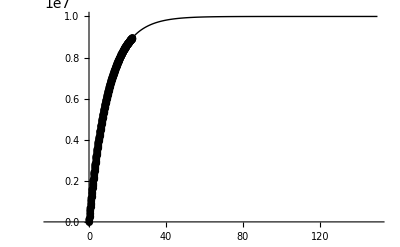

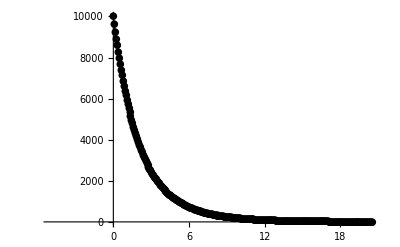

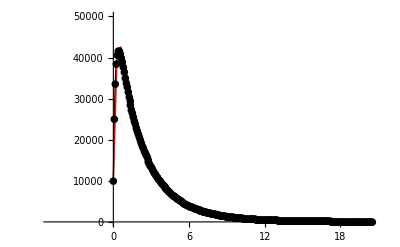

```mathematica
SolLst=LSteklov[150,500,Xzero];
Clear[g1,g2,g3];
XLst1=SolLst[[All,1]];
YLst1=SolLst[[All,2,1]];
XLst2=SolLst[[All,1]];
YLst2=SolLst[[All,2,2]];
XLst3=SolLst[[All,1]];
YLst3=SolLst[[All,2,3]];
SolLst1=Transpose[{XLst1[[1;;-1;;1]],YLst1[[1;;-1;;1]]}];
SolLst2=Transpose[{XLst2[[1;;-1;;1]],YLst2[[1;;-1;;1]]}];
SolLst3=Transpose[{XLst3[[1;;-1;;1]],YLst3[[1;;-1;;1]]}];
g1=ListPlot[
{Sol1,SolLst1},
PlotMarkers->{{●,10},{○,10}},
Joined->{True,False},
PlotStyle->{Black,Green},
PlotLegends->{Euler,Steklov},
PlotRange->{{-20,150},{0,10^7}}
]
g2=ListPlot[
{Sol2,SolLst2},
PlotMarkers->{{●,10},{○,10}},
Joined->{True,False},
PlotStyle->{Black,Green},
PlotLegends->{Euler,Steklov},
PlotRange->{{-5,20},{0,10000}}
]
g3=ListPlot[
{Sol3,SolLst3},
PlotMarkers->{{●,10},{○,10}},
Joined->{True,True},
PlotStyle->{Black,Red},
PlotLegends->{Euler,Steklov},
PlotRange->{{-5,20},{0,50000}}
]
```